## Integration of coupled scalar-tensor mode equation in kinetically-coupled dark energy

Author: Reggie Bernardo (rbernardo@nip.upd.edu.ph)

We integrate the equations obtained in the notebook “bald_bh_perturb.nb” for a dark matter particle falling straight into a Schwarzschild black hole.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["bald_bh_perturb.m"];
```

### I. Starting equations

The coupled-wave equation are given by...

```mathematica
ZerilliEquation
ψZerilli
```

(((6 M-3 r+r^3 Λ) (72 M^3+6 (-2+L+L^2)^2 M r^2+L (1+L) (-2+L+L^2)^2 r^3-12 M^2 r (6-3 L-3 L^2+2 r^2 Λ)))/(3 r^4 (6 M+(-2+L+L^2) r)^2)+ω^2) Kh[R[r]]-((6 M-3 r+r^3 Λ) (2 (6 M-3 r+r^3 Λ) t1[R[r]]+3 r (-r T2[R[r]]+(6 M+(-2+L+L^2) r) Tg[R[r]])))/(9 r (6 M+(-2+L+L^2) r) F[φ])+χ[R[r]] ((2 L (-2-L+2 L^2+L^3) (6 M-3 r+r^3 Λ) F'[φ])/(3 r (6 M+(-2+L+L^2) r)^2 F[φ])+(2 r ω^2 F'[φ])/((6 M+(-2+L+L^2) r) F[φ]))+(ⅈ (6 M-3 r+r^3 Λ) ((72 M^2+(-2+L+L^2) r^2 (3 L+3 L^2+4 r^2 Λ)+6 M r (-8+L+L^2+8 r^2 Λ)) t0[R[r]]+r (2 (18 M^2+(-2+L+L^2) r^4 Λ+3 M r (-4-L-L^2+4 r^2 Λ)) T1[R[r]]-3 r (6 M+(-2+L+L^2) r) (2 t0'[R[r]]+r T1'[R[r]]))))/(9 r^2 (6 M+(-2+L+L^2) r)^2 ω F[φ])-(8 M (6 M-3 r+r^3 Λ) F'[φ] χ'[R[r]])/(r (6 M+(-2+L+L^2) r)^2 F[φ])+Kh''[R[r]]+(2 r F'[φ] χ''[R[r]])/((6 M+(-2+L+L^2) r) F[φ])

-1/3 (6 M-3 r+r^3 Λ) (s T0[R[r]]-s T2[R[r]]+L s Tg[R[r]]+L^2 s Tg[R[r]]-2 s Tk[R[r]]-q δm[R[r]])+(((6 M-3 r+r^3 Λ) (6 M+r (3 L+3 L^2+r^2 (-2 Λ+3 μ^2))))/(9 r^4)+ω^2) χ[R[r]]+χ''[R[r]]

...where R(r) is the tortoise coordinate, i.e., ∂_r R=1/B(r). We shall focus on the Schwarzschild case, i.e., B(r)=1-2M/r and Λ=0. In this case, the above wave equations become...

```mathematica
CollectKψ[expr_]:=Collect[expr,{Kh[x_],Kh'[x_],Kh''[x_],χ[x_],χ'[x_],χ''[x_],ω^2},Simplify]

KZerilliSchw=ZerilliEquation/.Λ->0//CollectKψ;KZerilliSchw
ψZerilliSchw=ψZerilli/.Λ->0//CollectKψ;ψZerilliSchw
```

(((2 M-r) (72 M^3+36 (-2+L+L^2) M^2 r+6 (-2+L+L^2)^2 M r^2+L (1+L) (-2+L+L^2)^2 r^3))/(r^4 (6 M+(-2+L+L^2) r)^2)+ω^2) Kh[R[r]]-((2 M-r) ((4 M-2 r) t1[R[r]]+r (-r T2[R[r]]+(6 M+(-2+L+L^2) r) Tg[R[r]])))/(r (6 M+(-2+L+L^2) r) F[φ])+χ[R[r]] ((2 L (-2-L+2 L^2+L^3) (2 M-r) F'[φ])/(r (6 M+(-2+L+L^2) r)^2 F[φ])+(2 r ω^2 F'[φ])/((6 M+(-2+L+L^2) r) F[φ]))+(ⅈ (2 M-r) ((24 M^2+2 (-8+L+L^2) M r+L (-2-L+2 L^2+L^3) r^2) t0[R[r]]-r (2 M (-6 M+(4+L+L^2) r) T1[R[r]]+r (6 M+(-2+L+L^2) r) (2 t0'[R[r]]+r T1'[R[r]]))))/(r^2 (6 M+(-2+L+L^2) r)^2 ω F[φ])-(8 M (6 M-3 r) F'[φ] χ'[R[r]])/(r (6 M+(-2+L+L^2) r)^2 F[φ])+Kh''[R[r]]+(2 r F'[φ] χ''[R[r]])/((6 M+(-2+L+L^2) r) F[φ])

-(2 M-r) (s T0[R[r]]-s T2[R[r]]+L s Tg[R[r]]+L^2 s Tg[R[r]]-2 s Tk[R[r]]-q δm[R[r]])+(((2 M-r) (2 M+r (L+L^2+r^2 μ^2)))/r^4+ω^2) χ[R[r]]+χ''[R[r]]

The coefficients Ts are the components of the CDM’s SET. The decomposition is as follows...

```mathematica
NoBras={t[]->t,r[]->r,θ[]->θ,α[]->α};

"T_bc^(odd)"==(TO/.NoBras//MatrixForm)
"T_bc^(even)"==(TE/.NoBras//MatrixForm)
```

T_bc^(odd)==(0 | 0 | ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Csc[θ] PL[θ] tt0[r] | ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] tt0[r] PL'[θ]
0 | 0 | ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Csc[θ] PL[θ] tt1[r] | ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] tt1[r] PL'[θ]
ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Csc[θ] PL[θ] tt0[r] | ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Csc[θ] PL[θ] tt1[r] | tt2[r] (ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Cot[θ] Csc[θ] PL[θ]-ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Csc[θ] PL'[θ]) | 1/2 tt2[r] (-ⅇ^(-ⅈ m α-ⅈ t ω) m^2 Csc[θ] PL[θ]+ⅇ^(-ⅈ m α-ⅈ t ω) Cos[θ] PL'[θ]-ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] ((-L (1+L)+m^2 Csc[θ]^2) PL[θ]-Cot[θ] PL'[θ]))
ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] tt0[r] PL'[θ] | ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] tt1[r] PL'[θ] | 1/2 tt2[r] (-ⅇ^(-ⅈ m α-ⅈ t ω) m^2 Csc[θ] PL[θ]+ⅇ^(-ⅈ m α-ⅈ t ω) Cos[θ] PL'[θ]-ⅇ^(-ⅈ m α-ⅈ t ω) Sin[θ] ((-L (1+L)+m^2 Csc[θ]^2) PL[θ]-Cot[θ] PL'[θ])) | -tt2[r] (ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Cos[θ] PL[θ]-ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Sin[θ] PL'[θ]))

T_bc^(even)==(ⅇ^(-ⅈ m α-ⅈ t ω) B[r] PL[θ] T0[r] | ⅇ^(-ⅈ m α-ⅈ t ω) PL[θ] T1[r] | ⅇ^(-ⅈ m α-ⅈ t ω) t0[r] PL'[θ] | -ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL[θ] t0[r]
ⅇ^(-ⅈ m α-ⅈ t ω) PL[θ] T1[r] | (ⅇ^(-ⅈ m α-ⅈ t ω) PL[θ] T2[r])/B[r] | ⅇ^(-ⅈ m α-ⅈ t ω) t1[r] PL'[θ] | -ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL[θ] t1[r]
ⅇ^(-ⅈ m α-ⅈ t ω) t0[r] PL'[θ] | ⅇ^(-ⅈ m α-ⅈ t ω) t1[r] PL'[θ] | r^2 (ⅇ^(-ⅈ m α-ⅈ t ω) PL[θ] Tk[r]+ⅇ^(-ⅈ m α-ⅈ t ω) Tg[r] ((-L (1+L)+m^2 Csc[θ]^2) PL[θ]-Cot[θ] PL'[θ])) | r^2 Tg[r] (ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Cot[θ] PL[θ]-ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL'[θ])
-ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL[θ] t0[r] | -ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL[θ] t1[r] | r^2 Tg[r] (ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m Cot[θ] PL[θ]-ⅈ ⅇ^(-ⅈ m α-ⅈ t ω) m PL'[θ]) | r^2 (ⅇ^(-ⅈ m α-ⅈ t ω) PL[θ] Sin[θ]^2 Tk[r]+Tg[r] (-ⅇ^(-ⅈ m α-ⅈ t ω) m^2 PL[θ]+ⅇ^(-ⅈ m α-ⅈ t ω) Cos[θ] Sin[θ] PL'[θ])))

Also, δm(r) is defined by the decomposition δρ=δm(r)Y_lm where Y_lm are spherical harmonics. In principle, by providing the CDM source, or rather the Ts and δm, the waveforms K and ψ can be obtained.

For this notebook, we shall obtain the waveform for radially-falling CDM particles so that only the even parity modes will be triggered.

### II. Rewriting the wave equations

We specialize the wave equations to the case of a falling particle.

First, we revert the independent variable to the Schwarzschild coordinate r...

```mathematica
(* careful, apply reverse order *)
RTor0=expr_[R[r]]:>expr[r];
RTor1=expr_'[R[r]]:>B[r]expr'[r];
RTor2=expr_''[R[r]]:>B[r]D[(B[r]D[expr[r], r]), r];
```

The wave equations then become...

```mathematica
KZerilliSchwr=KZerilliSchw/.RTor2/.RTor1/.RTor0/.(SdS/.Λ->0)//CollectKψ;
ψZerilliSchwr=ψZerilliSchw/.RTor2/.RTor1/.RTor0/.(SdS/.Λ->0)//CollectKψ;

KZerilliSchwr
ψZerilliSchwr
```

(((2 M-r) (72 M^3+36 (-2+L+L^2) M^2 r+6 (-2+L+L^2)^2 M r^2+L (1+L) (-2+L+L^2)^2 r^3))/(r^4 (6 M+(-2+L+L^2) r)^2)+ω^2) Kh[r]-((2 M-r) ((4 M-2 r) t1[r]+r (-r T2[r]+(6 M+(-2+L+L^2) r) Tg[r])))/(r (6 M+(-2+L+L^2) r) F[φ])+χ[r] ((2 L (-2-L+2 L^2+L^3) (2 M-r) F'[φ])/(r (6 M+(-2+L+L^2) r)^2 F[φ])+(2 r ω^2 F'[φ])/((6 M+(-2+L+L^2) r) F[φ]))+(2 M (-2 M+r) Kh'[r])/r^3+(ⅈ (2 M-r) ((24 M^2+2 (-8+L+L^2) M r+L (-2-L+2 L^2+L^3) r^2) t0[r]-r (2 M (-6 M+(4+L+L^2) r) T1[r]-(2 M-r) (6 M+(-2+L+L^2) r) (2 t0'[r]+r T1'[r]))))/(r^2 (6 M+(-2+L+L^2) r)^2 ω F[φ])+(4 M (2 M-r) (6 M-(4+L+L^2) r) F'[φ] χ'[r])/(r^2 (6 M+(-2+L+L^2) r)^2 F[φ])+(1-(2 M)/r)^2 Kh''[r]+(2 (-2 M+r)^2 F'[φ] χ''[r])/(r (6 M+(-2+L+L^2) r) F[φ])

-(2 M-r) (s T0[r]-s T2[r]+L s Tg[r]+L^2 s Tg[r]-2 s Tk[r]-q δm[r])+(((2 M-r) (2 M+r (L+L^2+r^2 μ^2)))/r^4+ω^2) χ[r]+(2 M (-2 M+r) χ'[r])/r^3+(1-(2 M)/r)^2 χ''[r]

Now, for the radially-falling particle, the SET components are given by...

```mathematica
T0fp=T0->Function[r,(𝓂 ε)/(2π)E^(I ω T[r])/(r^2 B[r] √(1-(B[r]/ε^2)))Conjugate[SphericalHarmonicY[L,m,π/2,0]]];
T1fp=T1->Function[r,T0[r] √(1-(B[r]/ε^2))];
T2fp=T2->Function[r,T0[r](1-(B[r]/ε^2))];
Tsfp={t0->Function[r,0],t1->Function[r,0],Tk->Function[r,0],Tg->Function[r,0]};

δmfp=δm->Function[r,𝓂/(2π ε)E^(I ω T[r])/(r^2 √(1-(B[r]/ε^2)))Conjugate[SphericalHarmonicY[L,m,π/2,0]]];
```

The function B is given by the Schwarzschild metric...

```mathematica
"B(r)"==(B[r]/.SdS/.Λ->0)
```

B(r)==1-(2 M)/r

The function T(r) is given by...

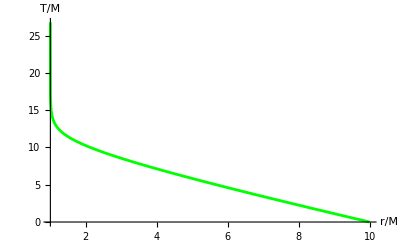

```mathematica
TfpInt=Integrate[-1/(B[r] √(1-(B[r]/ε^2)))/.(SdS/.Λ->0),r];

Tfp=T->Function[r,TfpInt-(TfpInt/.r->2M z)//Evaluate];

Plot[T[r]/.Tfp/.{M->1/2,ε->10,z->10},{r,1,10},PlotRange->All,AxesLabel->{"r/M","T/M"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotStyle->{Thickness[0.005],Green}]
```

...where z is the position of the particle (in units of 2M) at T=0.

To proceed, we identify the homogeneous wave equations...

```mathematica
KZerilliHom=KZerilliSchwr/.{T0->Function[r,0],T1->Function[r,0],T2->Function[r,0],t0->Function[r,0],t1->Function[r,0],Tk->Function[r,0],Tg->Function[r,0],χ->Function[r,0]};

ψZerilliHom=ψZerilliSchwr/.{T0->Function[r,0],T1->Function[r,0],T2->Function[r,0],t0->Function[r,0],t1->Function[r,0],Tk->Function[r,0],Tg->Function[r,0],δm->Function[r,0]};

KZerilliHom==0
ψZerilliHom==0
```

(((2 M-r) (72 M^3+36 (-2+L+L^2) M^2 r+6 (-2+L+L^2)^2 M r^2+L (1+L) (-2+L+L^2)^2 r^3))/(r^4 (6 M+(-2+L+L^2) r)^2)+ω^2) Kh[r]+(2 M (-2 M+r) Kh'[r])/r^3+(1-(2 M)/r)^2 Kh''[r]==0

(((2 M-r) (2 M+r (L+L^2+r^2 μ^2)))/r^4+ω^2) χ[r]+(2 M (-2 M+r) χ'[r])/r^3+(1-(2 M)/r)^2 χ''[r]==0

The source terms can be identified as...

```mathematica
KZerilliSource=SZ->Function[r,-KZerilliSchwr/.Solve[KZerilliHom==0,Kh''[r]][[1]]/.Tsfp];

ψZerilliSource=Sψ->Function[r,-ψZerilliSchwr/.Solve[ψZerilliHom==0,χ''[r]][[1]]/.Tsfp];

"S_Z(r)"==(SZ[r]/.KZerilliSource)
"S_ψ(r)"==(Sψ[r]/.ψZerilliSource)
```

S_Z(r)==-((2 M-r) r T2[r])/((6 M+(-2+L+L^2) r) F[φ])-χ[r] ((2 L (-2-L+2 L^2+L^3) (2 M-r) F'[φ])/(r (6 M+(-2+L+L^2) r)^2 F[φ])+(2 r ω^2 F'[φ])/((6 M+(-2+L+L^2) r) F[φ]))+(ⅈ (2 M-r) (2 M (-6 M+(4+L+L^2) r) T1[r]-(2 M-r) r (6 M+(-2+L+L^2) r) T1'[r]))/(r (6 M+(-2+L+L^2) r)^2 ω F[φ])-(4 M (2 M-r) (6 M-(4+L+L^2) r) F'[φ] χ'[r])/(r^2 (6 M+(-2+L+L^2) r)^2 F[φ])-(2 (-2 M+r)^2 F'[φ] χ''[r])/(r (6 M+(-2+L+L^2) r) F[φ])

S_ψ(r)==(2 M-r) (s T0[r]-s T2[r]-q δm[r])

### III. Asymptotics

The stability of the numerical integration requires some asymptotic solutions at the event horizon and infinity. This is derived in this section.

#### Asymptotic solutions of the Zerilli equation

It is obvious that the asymptotic solution, ψ~e^(i ω r_*), will take the form...

```mathematica
Oh=5;
Zeh[r_]=E^(I ω r)(r-2M)^(2M I ω)Sum[𝒯[n](r-2M)^n,{n,0,Oh}];
Zeqhor=(KZerilliHom/.Kh->Function[r,Zeh[r]])E^(-I ω r)(r-2M)^(-2M I ω)//Simplify;
Zsseqhor=Series[Zeqhor,{r,2M,Oh}];
Zeqshor=Table[SeriesCoefficient[Zsseqhor,n]==0,{n,1,Oh}];
Z𝒯eh=Table[𝒯[n],{n,1,Oh}];
Z𝒯sol=Simplify[Solve[Zeqshor,Z𝒯eh]][[1]];
```

To prove this is a solution, we can simply put it back...

```mathematica
Series[KZerilliHom/.Kh->Function[r,Zeh[r]]/.Z𝒯sol,{r,2M,Oh}]//Simplify
```

(-2 M+r)^(2 ⅈ M ω) O[r-2 M]^6

This is also sufficient to describe the wave falling down the hole, ψ~e^(-i ω r), with ω→-ω...

```mathematica
Series[KZerilliHom/.Kh->Function[r,(Zeh[r]/.ω->-ω)]/.(Z𝒯sol/.ω->-ω),{r,2M,Oh}]//Simplify
```

(-2 M+r)^(-2 ⅈ M ω) O[r-2 M]^6

At infinity, the asymptotic solution takes the form, ψ~e^(i ω r_*)/r. We derive the asymptotic coefficients below...

```mathematica
O∞=5;
Z∞[r_]=E^(I ω r)(r-2M)^(2M I ω)Sum[ℐ[n]/r^n,{n,0,O∞}];
Zeqinf=(KZerilliHom/.Kh->Function[r,Z∞[r]])E^(-I ω r)(r-2M)^(-2M I ω)//Simplify;
Zsseqinf=Series[Zeqinf,{r,∞,O∞+1}];Zeqsinf=Table[SeriesCoefficient[Zsseqinf,n]==0,{n,2,O∞+1}];
Zℐinf=Table[ℐ[n],{n,1,O∞}];
Zℐsol=Simplify[Solve[Zeqsinf,Zℐinf]][[1]];
```

To prove this is a solution, we simply plug it back...

```mathematica
Series[KZerilliHom/.Kh->Function[r,Z∞[r]]/.Zℐsol,{r,∞,O∞+1}]//Simplify
```

ⅇ^(ⅈ r ω) (-2 M+r)^(2 ⅈ M ω) O[1/r]^7

The incoming wave can equally be represented by the frequency-reflected version of this solution...

```mathematica
Series[KZerilliHom/.Kh->Function[r,Z∞[r]/.ω->-ω]/.(Zℐsol/.ω->-ω),{r,∞,O∞+1}]//Simplify
```

ⅇ^(-ⅈ r ω) (-2 M+r)^(-2 ⅈ M ω) O[1/r]^7

#### Asymptotic solutions of the massless scalar wave equation

We can obtain the asymptotic solutions of the massless scalar wave equation similarly. At the horizon, we obtain...

```mathematica
ψeh[r_]=E^(I ω r)(r-2M)^(2M I ω)Sum[𝓉[n](r-2M)^n,{n,0,Oh}];
ψeqhor=(ψZerilliHom/.μ->0/.χ->Function[r,ψeh[r]])E^(-I ω r)(r-2M)^(-2M I ω)//Simplify;
ψsseqhor=Series[ψeqhor,{r,2M,Oh}];
ψeqshor=Table[SeriesCoefficient[ψsseqhor,n]==0,{n,1,Oh}];
ψ𝓉eh=Table[𝓉[n],{n,1,Oh}];
ψ𝓉sol=Simplify[Solve[ψeqshor,ψ𝓉eh]][[1]];
```

This can be checked back into the wave equation...

```mathematica
Series[ψZerilliHom/.μ->0/.χ->Function[r,ψeh[r]]/.ψ𝓉sol,{r,2M,Oh}]//Simplify
```

(-2 M+r)^(2 ⅈ M ω) O[r-2 M]^6

This can also represent the falling wave...

```mathematica
Series[ψZerilliHom/.μ->0/.χ->Function[r,ψeh[r]/.ω->-ω]/.(ψ𝓉sol/.ω->-ω),{r,2M,Oh}]//Simplify
```

(-2 M+r)^(-2 ⅈ M ω) O[r-2 M]^6

At infinity, the asymptotic solution is given by...

```mathematica
ψ∞[r_]=E^(I ω r)(r-2M)^(2M I ω)Sum[𝒾[n]/r^n,{n,0,O∞}];
ψeqinf=(ψZerilliHom/.μ->0/.χ->Function[r,ψ∞[r]])E^(-I ω r)(r-2M)^(-2M I ω)//Simplify;
ψsseqinf=Series[ψeqinf,{r,∞,O∞+1}];ψeqsinf=Table[SeriesCoefficient[ψsseqinf,n]==0,{n,2,O∞+1}];
ψ𝒾inf=Table[𝒾[n],{n,1,O∞}];
ψ𝒾sol=Simplify[Solve[ψeqsinf,ψ𝒾inf]][[1]];
```

This can be easily checked...

```mathematica
Series[ψZerilliHom/.μ->0/.χ->Function[r,ψ∞[r]]/.ψ𝒾sol,{r,∞,O∞+1}]//Simplify
```

ⅇ^(ⅈ r ω) (-2 M+r)^(2 ⅈ M ω) O[1/r]^7

The incoming wave is given by the frequency-reflected version of the above solution...

```mathematica
Series[ψZerilliHom/.μ->0/.χ->Function[r,ψ∞[r]/.ω->-ω]/.(ψ𝒾sol/.ω->-ω),{r,∞,O∞+1}]//Simplify
```

ⅇ^(-ⅈ r ω) (-2 M+r)^(-2 ⅈ M ω) O[1/r]^7

#### Saving results

We save the results in this section so it will be possible to proceed with the numerical integration directly without going through all of the above subtleties. Saving...

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["integration_asymptotics.m",{KZerilliSchwr,ψZerilliSchwr,KZerilliHom,ψZerilliHom,KZerilliSource,ψZerilliSource,T0fp,T1fp,T2fp,Tsfp,δmfp,Zeh,Z𝒯sol,Z∞,Zℐsol,ψeh,ψ𝓉sol,ψ∞,ψ𝒾sol,Tfp}];*)
```

### IV. Numerical integration

Import equations to skip running Secs. I-III.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["integration_asymptotics.m"];
```

#### Boundary conditions

The boundary conditions for the Zerilli equation are...

```mathematica
(*transmitted down the hole*)
Zbc𝒯=Zeh[r]/.Z𝒯sol/.𝒯[0]->𝒯/.ω->-ω;

(*incident wave from infinity*)
Zbcℐ=Z∞[r]/.Zℐsol/.ℐ[0]->ℐ/.ω->-ω;

(*reflected back to infinity*)
Zbcℛ=Z∞[r]/.Zℐsol/.ℐ[0]->ℛ;

(*superposition at infinity*)
Zbcinf=Zbcℐ+Zbcℛ;
```

The boundary conditions for the scalar wave equation are...

```mathematica
(*transmitted down the hole*)
ψbc𝓉=ψeh[r]/.ψ𝓉sol/.𝓉[0]->𝓉/.ω->-ω;

(*incident wave from infinity*)
ψbc𝒾=ψ∞[r]/.ψ𝒾sol/.𝒾[0]->𝒾/.ω->-ω;

(*reflected back to infinity*)
ψbc𝓇=ψ∞[r]/.ψ𝒾sol/.𝒾[0]->𝓇;

(*superposition at infinity*)
ψbcinf=ψbc𝒾+ψbc𝓇;
```

#### Sources

We simplify the sources in preparation for the numerical integration. For the Zerilli equation, we separate the contributions coming from the CDM and dark energy...

```mathematica
ZsourceCDM=SZ[r]/.KZerilliSource/.χ->Function[r,0]/.T2fp/.T1fp/.T0fp/.T'[r]->-1/(B[r] √(1-(B[r]/ε^2)))/.B->Function[r,1-(2M)/r]/.Tfp//Simplify;

ZsourceDE=SZ[r]/.KZerilliSource/.T1->Function[r,0]/.T2->Function[r,0]//Simplify;
```

For the scalar wave equation...

```mathematica
ψsource=Sψ[r]/.ψZerilliSource/.T2fp/.T1fp/.T0fp/.δmfp/.B->Function[r,1-(2M)/r]/.Tfp//Simplify;
```

The integration over these sources will lead to the waveforms.

#### Numerical integration

Finally, we perform the numerical integration of the coupled scalar-tensor wave equations. This is performed below...

```mathematica
param={M->1/2,𝓂->1,q->-1,s->10^-2,ε->10,z->10,m->0,L->2,F[φ]->1/2,F'[φ]->10^-2};

reh=2M(1+10^-8);

ii=0;
Δ=1/100;
Nmax=100;

While[ii<6Nmax+1,
ω=(-3Nmax Δ)+(Δ ii)+10^-3;
rinf=100/Abs[ω];

(* solving scalar mode equation *)
χnsol=NDSolve[{ψZerilliHom==0/.μ->0/.param,χ[(reh/.param)]==(ψbc𝓉/.𝓉->1/.r->reh/.param),χ'[(reh/.param)]==((D[ψbc𝓉, r])/.𝓉->1/.r->reh/.param)},χ,{r,reh/.param,rinf},WorkingPrecision->30];

χnsolPart=NDSolve[{ψZerilliHom==ψsource/.μ->0/.param,χ[(reh/.param)]==(ψbc𝓉/.𝓉->1/.r->reh/.param),χ'[(reh/.param)]==((D[ψbc𝓉, r])/.𝓉->1/.r->reh/.param)},χ,{r,reh/.param,rinf},WorkingPrecision->30];

χninf=χ[rinf]/.χnsol[[1]];
Dχninf=χ'[rinf]/.χnsol[[1]];

𝒾𝓇sol=Solve[{χninf==ψbcinf,Dχninf==(D[ψbcinf, r])}/.r->rinf/.param,{𝒾,𝓇}][[1]];

(* solving Zerilli equation *)
Knsol=NDSolve[{KZerilliHom==0/.param,Kh[(reh/.param)]==(Zbc𝒯/.𝒯->1/.r->reh/.param),Kh'[(reh/.param)]==((D[Zbc𝒯, r])/.𝒯->1/.r->reh/.param)},Kh,{r,reh/.param,rinf}];

Kninf=Kh[rinf]/.Knsol[[1]];
DKninf=Kh'[rinf]/.Knsol[[1]];

ℐℛsol=Solve[{Kninf==Zbcinf,DKninf==(D[Zbcinf, r])}/.r->rinf/.param,{ℐ,ℛ}][[1]];

(* scalar mode output ψ(ω) *)
ψrinf=NIntegrate[ψsource/(1-(2M/r))χ[r]/.param/.χnsol,{r,(reh/.param),rinf},WorkingPrecision->10,MaxRecursion->30][[1]];
Aψrinf=I/(2 ω 𝒾)(rinf-2M)^(2I M ω)E^(I ω rinf)/.param/.𝒾𝓇sol;

(* tensor mode output K̂(ω) *)
KrinfCDM=NIntegrate[ZsourceCDM/(1-(2M/r))Kh[r]/.param/.Knsol,{r,(reh/.param),rinf},WorkingPrecision->10,MaxRecursion->30][[1]];
KrinfDEPart=NIntegrate[ZsourceDE/(1-(2M/r))Kh[r]/.param/.χnsolPart[[1]]/.Knsol,{r,(reh/.param),rinf},Method->"DoubleExponential",AccuracyGoal->5,MaxRecursion->100][[1]];
KrinfDEHom=NIntegrate[ZsourceDE/(1-(2M/r))Kh[r]/.param/.χnsol[[1]]/.Knsol,{r,(reh/.param),rinf},Method->"DoubleExponential",AccuracyGoal->5,MaxRecursion->100][[1]];
AKrinf=I/(2 ω ℐ)(rinf-2M)^(2I M ω)E^(I ω rinf)/.param/.ℐℛsol;

(* for tracking *)
If[ii==Round[0.1*6Nmax],Print["10 percent"]];
If[ii==Round[0.2*6Nmax],Print["20 percent"]];
If[ii==Round[0.3*6Nmax],Print["30 percent"]];
If[ii==Round[0.4*6Nmax],Print["40 percent"]];
If[ii==Round[0.5*6Nmax],Print["50 percent"]];
If[ii==Round[0.6*6Nmax],Print["60 percent"]];
If[ii==Round[0.7*6Nmax],Print["70 percent"]];
If[ii==Round[0.8*6Nmax],Print["80 percent"]];
If[ii==Round[0.9*6Nmax],Print["90 percent"]];

(* save as "Intlxqy"<> for l = x & q = y *)
Intl2q1neg[ii]={ω,Aψrinf ψrinf,AKrinf KrinfCDM,AKrinf (KrinfDEPart-KrinfDEHom)};
ii++];
```

10 percent

20 percent

30 percent

40 percent

50 percent

60 percent

70 percent

80 percent

90 percent

Save results...

```mathematica
(*SetDirectory[NotebookDirectory[]];
DumpSave["int_result_l2_q1neg.m",{Intl2q1neg,Nmax,param}];*)
```

This section should be done for q=0,1, and -1 with results saved as int_result _l2 _q0.m, int_result _l2 _q1pls.m, and int_result _l2 _q1neg.m, respectively.

#### Analysis for l=2: frequency- and time-domain waveforms

We start with the waveforms for l=2. Importing the results...

```mathematica
SetDirectory[NotebookDirectory[]];
Get["int_result_l2_q0.m"]
Get["int_result_l2_q1pls.m"]
Get["int_result_l2_q1neg.m"]
```

The power spectrum from the different contributions can be obtained using the following line...

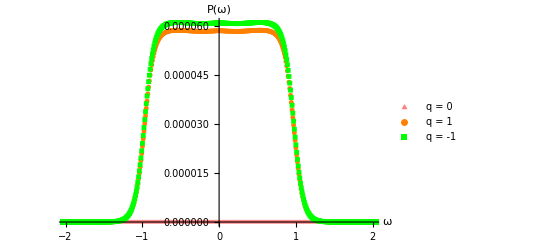

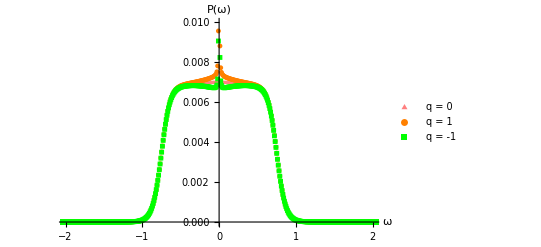

```mathematica
IntTabl2q0=Table[Intl2q0[ii],{ii,0Nmax,6Nmax}];
IntTabl2q1pls=Table[Intl2q1pls[ii],{ii,0Nmax,6Nmax}];
IntTabl2q1neg=Table[Intl2q1neg[ii],{ii,0Nmax,6Nmax}];

(* scalar power spectrum *)
PSψl2q0=Table[{IntTabl2q0[[i,1]],IntTabl2q0[[i,1]]^2 Abs[IntTabl2q0[[i,2]]]^2},{i,1,Length[IntTabl2q0]}];
PSψl2q1pls=Table[{IntTabl2q1pls[[i,1]],IntTabl2q1pls[[i,1]]^2 Abs[IntTabl2q1pls[[i,2]]]^2},{i,1,Length[IntTabl2q1pls]}];
PSψl2q1neg=Table[{IntTabl2q1neg[[i,1]],IntTabl2q1neg[[i,1]]^2 Abs[IntTabl2q1neg[[i,2]]]^2},{i,1,Length[IntTabl2q1neg]}];

(* tensor power spectrum *)
PShl2q0=Table[{IntTabl2q0[[i,1]],IntTabl2q0[[i,1]]^2 Abs[IntTabl2q0[[i,3]]+IntTabl2q0[[i,4]]]^2},{i,1,Length[IntTabl2q0]}];
PShl2q1pls=Table[{IntTabl2q1pls[[i,1]],IntTabl2q1pls[[i,1]]^2 Abs[IntTabl2q1pls[[i,3]]+IntTabl2q1pls[[i,4]]]^2},{i,1,Length[IntTabl2q1pls]}];
PShl2q1neg=Table[{IntTabl2q1neg[[i,1]],IntTabl2q1neg[[i,1]]^2 Abs[IntTabl2q1neg[[i,3]]+IntTabl2q1neg[[i,4]]]^2},{i,1,Length[IntTabl2q1neg]}];

ListPlot[{PSψl2q0,PSψl2q1pls,PSψl2q1neg},PlotRange->{{-2,2},Automatic},AxesLabel->{"ω","P(ω)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotMarkers->{{▲,5},{●,5},{■,5}},PlotStyle->{Pink,Orange,Green}]

ListPlot[{PShl2q0,PShl2q1pls,PShl2q1neg},PlotRange->{{-2,2},{0,0.01}},AxesLabel->{"ω","P(ω)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotMarkers->{{▲,5},{●,5},{■,5}},PlotStyle->{Pink,Orange,Green}]
```

It will be useful to construct the interpolated versions of the power spectrum. This is done below...

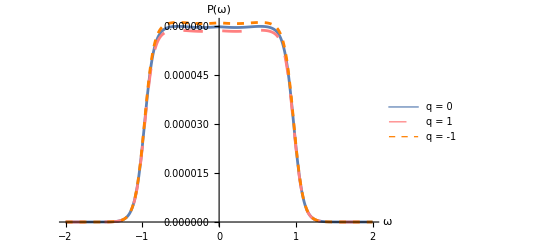

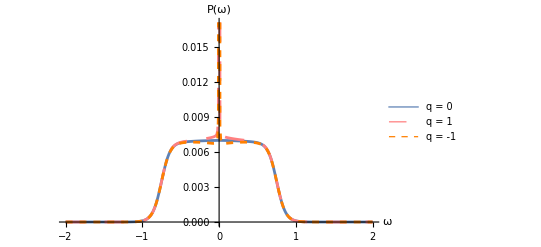

```mathematica
PSψl2q0Smooth=Interpolation[PSψl2q0];
PSψl2q1plsSmooth=Interpolation[PSψl2q1pls];
PSψl2q1negSmooth=Interpolation[PSψl2q1neg];

PShl2q0Smooth=Interpolation[PShl2q0,InterpolationOrder->1];
PShl2q1plsSmooth=Interpolation[PShl2q1pls,InterpolationOrder->1];
PShl2q1negSmooth=Interpolation[PShl2q1neg,InterpolationOrder->1];

Plot[{10^4 PSψl2q0Smooth[ω],PSψl2q1plsSmooth[ω],PSψl2q1negSmooth[ω]},{ω,-2,2},AxesLabel->{"ω","P(ω)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]

Plot[{PShl2q0Smooth[ω],PShl2q1plsSmooth[ω],PShl2q1negSmooth[ω]},{ω,-2,2},AxesLabel->{"ω","P(ω)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]
```

Now, we plot the Fourier domain waveforms...

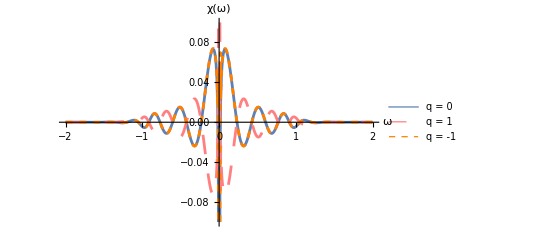

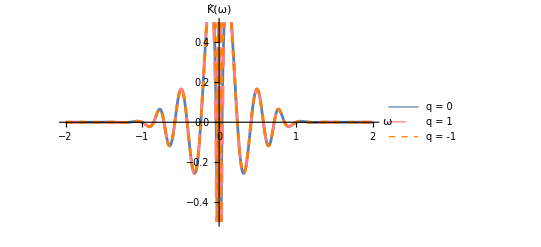

```mathematica
(* frequency-domain waveform q = 0 *)
ψfdl2q0=Table[{IntTabl2q0[[i,1]],IntTabl2q0[[i,2]]},{i,1,Length[IntTabl2q0]}];
hfdl2q0=Table[{IntTabl2q0[[i,1]],IntTabl2q0[[i,3]]+IntTabl2q0[[i,4]]},{i,1,Length[IntTabl2q0]}];

(* frequency-domain waveform q = 1 *)
ψfdl2q1pls=Table[{IntTabl2q1pls[[i,1]],IntTabl2q1pls[[i,2]]},{i,1,Length[IntTabl2q1pls]}];
hfdl2q1pls=Table[{IntTabl2q1pls[[i,1]],IntTabl2q1pls[[i,3]]+IntTabl2q1pls[[i,4]]},{i,1,Length[IntTabl2q1pls]}];

(* frequency-domain waveform q = -1 *)
ψfdl2q1neg=Table[{IntTabl2q1neg[[i,1]],IntTabl2q1neg[[i,2]]},{i,1,Length[IntTabl2q1neg]}];
hfdl2q1neg=Table[{IntTabl2q1neg[[i,1]],IntTabl2q1neg[[i,3]]+IntTabl2q1neg[[i,4]]},{i,1,Length[IntTabl2q1neg]}];

ψfdl2q0Smooth=Interpolation[ψfdl2q0,InterpolationOrder->1];
hfdl2q0Smooth=Interpolation[hfdl2q0,InterpolationOrder->1];

ψfdl2q1plsSmooth=Interpolation[ψfdl2q1pls];
hfdl2q1plsSmooth=Interpolation[hfdl2q1pls];

ψfdl2q1negSmooth=Interpolation[ψfdl2q1neg];
hfdl2q1negSmooth=Interpolation[hfdl2q1neg];

Plot[{10^2 Re[ψfdl2q0Smooth[ω]],Re[ψfdl2q1plsSmooth[ω]],Re[ψfdl2q1negSmooth[ω]]},{ω,-2,2},AxesLabel->{"ω","χ(ω)"},PlotRange->{Automatic,{-0.1,0.1}},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]

Plot[{Re[hfdl2q0Smooth[ω]],Re[hfdl2q1plsSmooth[ω]],Re[hfdl2q1negSmooth[ω]]},{ω,-2,2},AxesLabel->{"ω","K̂(ω)"},PlotRange->{Automatic,{-0.5,0.5}},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]
```

To get the time-domain waveforms, we perform the Fourier inversion. This is done in the next line...

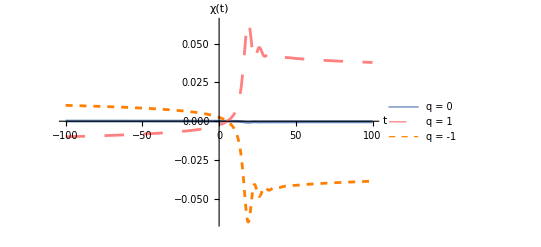

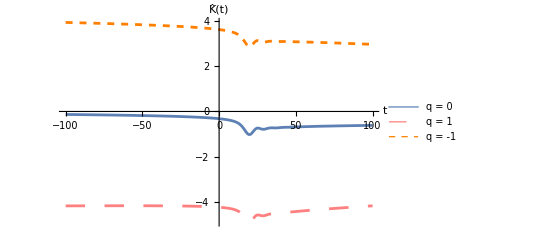

```mathematica
(* time domain waveforms q = 0 *)
ψtdl2q0[t_]:=Sum[ψfdl2q0[[i,2]]Exp[-I ψfdl2q0[[i,1]]t](ψfdl2q0[[i+1,1]]-ψfdl2q0[[i,1]]),{i,1,Length[ψfdl2q0]-1}];
htdl2q0[t_]:=Sum[hfdl2q0[[i,2]]Exp[-I hfdl2q0[[i,1]]t](hfdl2q0[[i+1,1]]-hfdl2q0[[i,1]]),{i,1,Length[hfdl2q0]-1}];

(* time domain waveforms q = 1 *)
ψtdl2q1pls[t_]:=Sum[ψfdl2q1pls[[i,2]]Exp[-I ψfdl2q1pls[[i,1]]t](ψfdl2q1pls[[i+1,1]]-ψfdl2q1pls[[i,1]]),{i,1,Length[ψfdl2q1pls]-1}];
htdl2q1pls[t_]:=Sum[hfdl2q1pls[[i,2]]Exp[-I hfdl2q1pls[[i,1]]t](hfdl2q1pls[[i+1,1]]-hfdl2q1pls[[i,1]]),{i,1,Length[hfdl2q1pls]-1}];

(* time domain waveforms q = -1 *)
ψtdl2q1neg[t_]:=Sum[ψfdl2q1neg[[i,2]]Exp[-I ψfdl2q1neg[[i,1]]t](ψfdl2q1neg[[i+1,1]]-ψfdl2q1neg[[i,1]]),{i,1,Length[ψfdl2q1neg]-1}];
htdl2q1neg[t_]:=Sum[hfdl2q1neg[[i,2]]Exp[-I hfdl2q1neg[[i,1]]t](hfdl2q1neg[[i+1,1]]-hfdl2q1neg[[i,1]]),{i,1,Length[hfdl2q1neg]-1}];

Plot[{Re[ψtdl2q0[t]],Re[ψtdl2q1pls[t]],Re[ψtdl2q1neg[t]]},{t,-100,100},PlotRange->All,AxesLabel->{"t","χ(t)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]

Plot[{Re[htdl2q0[t]],Re[htdl2q1pls[t]],Re[htdl2q1neg[t]]},{t,-100,100},PlotRange->All,AxesLabel->{"t","K̂(t)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]
```

We can see from this that the waveforms themselves will not be easy to compare because of the differences in overall orientation. We resolve this below by making the orientations at the early t similar...

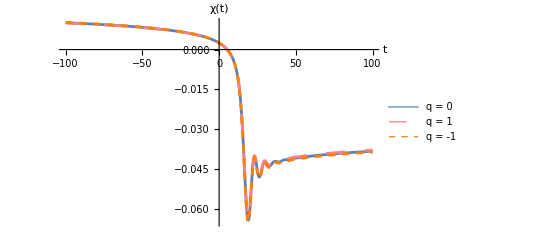

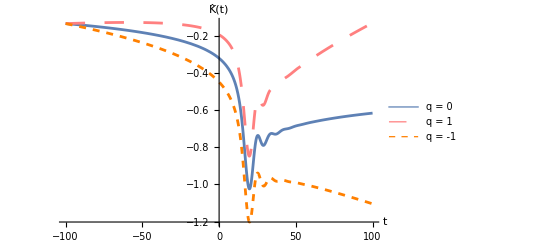

```mathematica
(* scalar waveforms *)
Plot[{100Re[ψtdl2q0[t]],-Re[ψtdl2q1pls[t]],Re[ψtdl2q1neg[t]]},{t,-100,100},PlotRange->All,AxesLabel->{"t","χ(t)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->{Automatic,Automatic},TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]

(* metric waveforms *)
Plot[{Re[htdl2q0[t]],Re[htdl2q1pls[t]]+(Re[htdl2q0[-100]]-Re[htdl2q1pls[-100]]),Re[htdl2q1neg[t]]-(Re[htdl2q1neg[-100]]-Re[htdl2q0[-100]])},{t,-100,100},PlotRange->All,AxesLabel->{"t","K̂(t)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->{Automatic,Automatic},TicksStyle->Directive[Red,15],PlotLegends->{"q = 0","q = 1","q = -1"},PlotStyle->{{Thickness[0.005]},{Dashing[Large],Thickness[0.005],Pink},{Dashing[Small],Thickness[0.005],Orange}}]
```